```mathematica
Needs["Combinatorica`"];
Dseries[nSer_]:=Module[{i,j,p0,p,ρ,n,s,counts,key,val,delPart,orbit,dimO,dimM,dt,Γ1,Γ2,Γs,HS,HWG,mHL,DseriesModuli,Labels,DseriesModuliTable},
n=2nSer;
DseriesModuli={};
p0= IntegerPartitions[n];
(*delete some partitions*)
p={};
For[i=1,i≤Length[p0],i++,
counts=Counts[p0⟦i⟧];
key=Keys[counts];
val=Values[counts];
delPart=Or@@Table[EvenQ[key⟦j⟧]&&OddQ[val⟦j⟧],{j,1,Length[key]}];
If[Not[delPart],AppendTo[p,p0⟦i⟧]]
];
ρ=Table[TransposePartition[p⟦i⟧],{i,1,Length[p]}];
s=Table[Table[0,{Length[TransposePartition[p⟦i⟧]]}],{i,1,Length[p]}];
For[i=1,i≤ Length[p], i++,
(*Orbit*)
counts=Counts[p⟦i⟧];
key=Keys[counts];
val=Values[counts];
orbit=Table[If[val⟦k⟧==1,key⟦k⟧,Superscript[key⟦k⟧,val⟦k⟧]],{k,1,Length[key]}];
If[(And@@EvenQ[key])&&(And@@EvenQ[val]), orbit=Superscript [orbit,"I/II"]];(*very even partition*)
(*dim(O)*)
dimO=n(n-1)/2-Sum[ρ⟦i,j⟧(ρ⟦i,j⟧-1),{j,1,Length[ρ⟦i⟧],2}]/2-Sum[ρ⟦i,j⟧(ρ⟦i,j⟧+1),{j,2,Length[ρ⟦i⟧],2}]/2;
(*dimO=(n(n-1))/2-(∑_(j=2)^Length[ρ⟦i⟧] ((ρ⟦i,j⟧(ρ⟦i,j⟧-1))Mod[j,2]))/2-(∑_(j = 2)^Length[ρ⟦i⟧] ((ρ⟦i,j⟧(ρ⟦i,j⟧+1))Mod[j,2]))/2;*)
(*dim(M_H)*)
dimM=dimO/2;
(*string d^t*)
counts=Counts[ρ⟦i⟧];
key=Keys[counts];
val=Values[counts];
dt=Table[
If[val⟦k⟧==1,key⟦k⟧,Superscript[key⟦k⟧,val⟦k⟧]],
{k,1,Length[key]}];
(*Γ1*)
For[j=1,j≤ Length[s⟦i⟧], j++,
If[j==1,s⟦i,j⟧=n-ρ⟦i,j⟧,s⟦i,j⟧=s⟦i,j-1⟧-ρ⟦i,j⟧];
];
dx = 3;
r =1;
Γ1=Graphics[{
{EdgeForm[{Thin,Blue}],White,Rectangle[{dx-r,dx+r+0.5},{dx+r,r+0.5}]},
If[i< Length [p],Line[{{dx,dx-3/2 r},{dx,dx-r}}]],
{Darker[Green],Table[Circle[{(k-1) dx,0},r],{k,3,Length[s[[i]]],2}]},
{Darker[Yellow],Table[Circle[{(k-1) dx,0},r],{k,2,Length[s[[i]]],2}]},
Table[Line[{{(k-2) dx+r,0},{(k-1) dx-r,0}}],{k,3,Length[s⟦i⟧]}],
Table[Text[s⟦i,k-1⟧,{(k-1) dx,0}],{k,2,Length[s[[i]]]}],
Text[n,{dx,dx+r/2}]
},ImageSize->{15n,40}];


(*Γ2*)
(*WANT TO DEFINE Γ2 based on mirror transitions*)

ϕ = 1;
κ =0;
ν=0;
σ =2;
α =β =γ =δ = 1;
δϕ=αϕ = βϕ = γϕ =1 ;
δγ=αγ = βγ = γγ =1 ;
Γ = Table[1,nSer-2];
(*Minimal*)
If[OddQ[nSer],{κ = 2}]  ;
If[EvenQ[nSer],{κ = 1,ϕ=1}]  ;

If [dimO ==(4nSer -6), {If[nSer≠  3,γγ =2],ν =2,{If[OddQ[nSer],{γ = 0},{α =0,β =0,Γ⟦nSer-2⟧=2}], δ  = 0}}];
(*SupraMinimal*)
If [dimO ==(4nSer -4), {γγ =2,ν =2,β =0, α  = 0,δ =1,γ =0,Γ = Table[2,nSer-2],δϕ =2}];


(*If [dimO ==(4nSer -4), {ν =2,ϕ=2,ν = 1,For[j = 1, j < Length[γ],j++,γ⟦j⟧= 2];}];*)
If[ ν > 0,
Γ2=Graphics[{

{Black, Line[{{σ (nSer-2) dx ,0},{σ (nSer-1)dx-κ ,2r}}]},
{Black,Line[{{ σ(nSer-2) dx ,0},{σ(nSer-1)dx -κ,-2r}}]},
{Black, Line[{{σ dx δ,0},{(σ dx -4r)δ,0}}]},

{Black, Line[{{(σ (nSer-1)dx-κ )β,2r β},{((nSer-1)σ dx +2r)β,2r β}}]},
{Black, Line[{{(σ(nSer-2)dx)γ ,0},{((nSer-1)σ dx +2r)γ,0}}]},
{Black,Line[{  {(σ(nSer-1)dx -κ),-2r}α,{((nSer-1)σ dx +2r)α,-2r α}}]},
{Black,Line[{{ σ dx,0},{(nSer-2)σ dx ,0}}]},

{Blue,Table[Disk[{σ k dx,0},r],{k,1,nSer-3}]},
{Blue,Disk[{σ( nSer-1) dx-κ,2r },r]},
{Blue,Disk[{σ( nSer-2) dx,0},r]},
{Blue,Disk[{σ ( nSer-1) dx-κ,-2r },r]},

{Red, Rectangle[{(σ(nSer-1) dx+2r)β,3r β},{(σ( nSer-1)dx+4r)β,r β}]},
{Red, Rectangle[{(σ(nSer-1) dx+2r)γ,-r γ},{(σ( nSer-1) dx+4r)γ,r γ}]},
{Red, Rectangle[{(σ(nSer-1) dx+2r)α,-3r α},{(σ( nSer-1) dx+4r)α,-r α}]},
{Red, Rectangle[{(σ dx-6r)δ,-r δ},{(σ dx-4r) δ,r δ}]},

Table[Style[Text[Γ⟦k⟧,{σ k dx,0}],White],{k,nSer-3}],

Style[Text[ϕ,{(σ(nSer-1) dx-κ),2r }],White],
Style[Text[ϕ,{(σ(nSer-1) dx+3r),2r }],White],

Style[Text[ϕ,{(σ(nSer-1) dx+3r),0}],White],
Style[Text[γγ,{(σ(nSer-2) dx),0}],White],

Style[Text[ϕ,{(σ(nSer-1) dx+-κ),-2r }],White],
Style[Text[ϕ,{(σ(nSer-1) dx+3r),-2r }],White],

Style[Text[δϕ,{(σ dx-5r)δ, 0}],White]


}(*ImageSize->{15n,40}*)];
,Γ2=nSer];


(*Subscript[Γ, Santi]*)
ι =φ =1;
If[OddQ[nSer],{ι = 1,φ =2},{ι = 2,φ =1}];

Γs =Graphics[{
{Black, Line[{{(σ dx) ,0},{(n σ dx),0}}]},
{Darker[Yellow],Table[Disk[{σ k dx,0},r],{k,ι,n,2}]},
{Darker[Green],Table[Disk[{σ k dx,0},r],{k,φ,n,2}]}
}];


(*Defined Hilbert Series for all D Series moduli spaces*)
If[ i==1, HS=(2-t^(2nSer))(∏_(i=1)^(nSer-1) (1-t^(4i)))/((1-t^2)^(nSer(2nSer-1)))];
If [i>=2 ,HS=("polynom")/((1-t^2)^dimO)];
If [i==Length[p] ,HS=1];
(*Character HWG definition*)
If[i<Length[p]-3,HWG="..."];
If[i==Length[p]-2, HWG=1/((1-Subscript[m, 2] t^2)(1-Subscript[m, 1]^2 t^4))];
If[i==Length[p]-1, HWG=1/(1-Subscript[m, 2]^2 t^2)];
If[i==Length[p], HWG=1];

If[ Length[s⟦i⟧]==2,
Which[
nSer≥  2(s⟦i,1⟧/2+1),   HWG=1/(∏_(l =1)^(s⟦i,1⟧/2) (1-Subscript[m, 2l] t^(2l))) ,
nSer== 2(s⟦i,1⟧/2+1/2), HWG=1/(∏_(l =1)^(s⟦i,1⟧/2-1) ((1-Subscript[m, 2l] t^(2l))(1-Subscript[m, nSer-1]^2 Subscript[m, nSer] t^(nSer-1)))),
 nSer== s⟦i,1⟧,HWG=(1-Subscript[m, nSer-1]^2 Subscript[m, nSer]^2 t^(2nSer))/((∏_(l =1)^(s⟦i,1⟧/2-1) (1-Subscript[m, 2l] t^(2l)))(1-Subscript[m, nSer-1]^2 t^nSer)(1-Subscript[m, nSer]^2 t^nSer))
];
];


(*modified Hall-Littelwood HWG function definition*)
If[i==1, mHL=1];
If[i==2,mHL=1-Subscript[h, nSer-1] Subscript[h, nSer] t^(2nSer)];
If[i>2,mHL="..."];
(*Want to define from Hanany Kalveks patterns, need to implement that*)

AppendTo[DseriesModuli,{orbit,dimO,dimM,dt,Γ1,Γ2,Γs,HS,HWG,mHL}]
];
DseriesModuli=Sort[DseriesModuli,#1[[2]]<#2[[2]]&];(*sort by dimO*)
Labels={{"Orbit","dim(O)","dim(ℳ_H)^ℍ","d^t","Γ_1","Γ_2^R","Γ_2^S","Higgs HS","Character HWG","mHL HWG"}};
DseriesModuliTable=Join[Labels,DseriesModuli];
Labeled[Grid[DseriesModuliTable,Frame->All,Background->{None,{LightRed}},ItemSize->{Automatic,2},Alignment->Left],"Quivers for Nilpotent Orbits of "<>ToString[Subscript["D",nSer],TraditionalForm],Top]
]
```

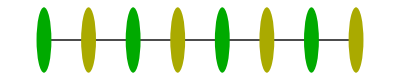
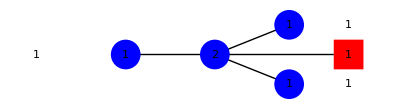
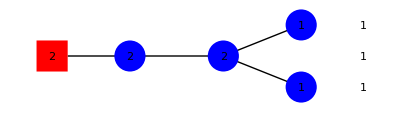
Orbit | dim(O) | dim(ℳ_H)^ℍ | d^t | Γ_1 | Γ_2^R | Γ_2^S | Higgs HS | Character HWG | mHL HWG
{1^8} | 0 | 0 | {8} | -Graphics- | 4 | -Graphics- | 1 | 1 | ...
{2^2,1^4} | 10 | 5 | {6,2} | -Graphics- | -Graphics- | -Graphics- | polynom/((1-t^2)^10) | 1/(1-t^2 m_2) | ...
{2^4}^(I/II) | 12 | 6 | {4^2} | -Graphics- | -Graphics- | -Graphics- | polynom/((1-t^2)^12) | (1-t^8 m_3^2 m_4^2)/((1-t^2 m_2) (1-t^4 m_3^2) (1-t^4 m_4^2)) | ...
{3,1^5} | 12 | 6 | {6,1^2} | -Graphics- | -Graphics- | -Graphics- | polynom/((1-t^2)^12) | ... | ...
{3,2^2,1} | 16 | 8 | {4,3,1} | -Graphics- | 4 | -Graphics- | polynom/((1-t^2)^16) | ... | ...
{3^2,1^2} | 18 | 9 | {4,2^2} | -Graphics- | 4 | -Graphics- | polynom/((1-t^2)^18) | ... | ...
{4^2}^(I/II) | 20 | 10 | {2^4} | -Graphics- | 4 | -Graphics- | polynom/((1-t^2)^20) | ... | ...
{5,1^3} | 20 | 10 | {4,1^4} | -Graphics- | 4 | -Graphics- | polynom/((1-t^2)^20) | ... | ...
{5,3} | 22 | 11 | {2^3,1^2} | -Graphics- | 4 | -Graphics- | polynom/((1-t^2)^22) | ... | 1-t^8 h_3 h_4
{7,1} | 24 | 12 | {2,1^6} | -Graphics- | 4 | -Graphics- | ((1-t^4) (1-t^8) (2-t^8) (1-t^12))/((1-t^2)^28) | ... | 1Quivers for Nilpotent Orbits of D_4

```mathematica
Dseries[4]
```